Wolfram Online Mini Campus. Part 21

Instagram Posts
Pinterest Posts
"Translation" of 📑 SageMath Online Mini Campus. Part 21
http://www.wolfram.com/broadcast/video.php?c=460&v=2672
https://blog.stephenwolfram.com/2019/04/version-12-launches-today-big-jump-for-wolfram-language-and-mathematica/
https://sparse.tamu.edu/

Graphs & Matrix as Creativity Expression

```mathematica
ExampleData["Matrix"][[1551;;1700,2]]
```

{MHD4800B,Mittelmann/cont11_l,Mittelmann/cont1_l,Mittelmann/fome11,Mittelmann/fome12,Mittelmann/fome13,Mittelmann/fome20,Mittelmann/fome21,Mittelmann/neos,Mittelmann/neos1,Mittelmann/neos2,Mittelmann/neos3,Mittelmann/nug08-3rd,Mittelmann/pds-100,Mittelmann/pds-30,Mittelmann/pds-40,Mittelmann/pds-50,Mittelmann/pds-60,Mittelmann/pds-70,Mittelmann/pds-80,Mittelmann/pds-90,Mittelmann/rail2586,Mittelmann/rail4284,Mittelmann/rail507,Mittelmann/rail516,Mittelmann/rail582,Mittelmann/sgpf5y6,Mittelmann/spal_004,Mittelmann/stormG2_1000,Mittelmann/watson_1,Mittelmann/watson_2,MKS/fp,Morandini/robot,Morandini/rotor1,Morandini/rotor2,Mulvey/finan512,Mulvey/pfinan512,Nasa/barth,Nasa/barth4,Nasa/barth5,Nasa/nasa1824,Nasa/nasa2146,Nasa/nasa2910,Nasa/nasa4704,Nasa/nasasrb,Nasa/pwt,Nasa/shuttle_eddy,Nasa/skirt,ND/nd12k,ND/nd24k,ND/nd3k,ND/nd6k,Nemeth/nemeth01,Nemeth/nemeth02,Nemeth/nemeth03,Nemeth/nemeth04,Nemeth/nemeth05,Nemeth/nemeth06,Nemeth/nemeth07,Nemeth/nemeth08,Nemeth/nemeth09,Nemeth/nemeth10,Nemeth/nemeth11,Nemeth/nemeth12,Nemeth/nemeth13,Nemeth/nemeth14,Nemeth/nemeth15,Nemeth/nemeth16,Nemeth/nemeth17,Nemeth/nemeth18,Nemeth/nemeth19,Nemeth/nemeth20,Nemeth/nemeth21,Nemeth/nemeth22,Nemeth/nemeth23,Nemeth/nemeth24,Nemeth/nemeth25,Nemeth/nemeth26,NNC1374,NNC261,NNC666,Norris/fv1,Norris/fv2,Norris/fv3,Norris/heart1,Norris/heart2,Norris/heart3,Norris/lung1,Norris/lung2,Norris/stomach,Norris/torso1,Norris/torso2,Norris/torso3,NOS1,NOS2,NOS3,NOS4,NOS5,NOS6,NOS7,Oberwolfach/bone010,Oberwolfach/boneS01,Oberwolfach/boneS10,Oberwolfach/chipcool0,Oberwolfach/chipcool1,Oberwolfach/filter2D,Oberwolfach/filter3D,Oberwolfach/flowmeter0,Oberwolfach/flowmeter5,Oberwolfach/gas_sensor,Oberwolfach/gyro,Oberwolfach/gyro_k,Oberwolfach/gyro_m,Oberwolfach/inlet,Oberwolfach/LF10,Oberwolfach/LF10000,Oberwolfach/LFAT5,Oberwolfach/LFAT5000,Oberwolfach/piston,Oberwolfach/rail_1357,Oberwolfach/rail_20209,Oberwolfach/rail_5177,Oberwolfach/rail_79841,Oberwolfach/spiral,Oberwolfach/t2dah,Oberwolfach/t2dah_a,Oberwolfach/t2dah_e,Oberwolfach/t2dal,Oberwolfach/t2dal_a,Oberwolfach/t2dal_bci,Oberwolfach/t2dal_e,Oberwolfach/t3dh,Oberwolfach/t3dh_a,Oberwolfach/t3dh_e,Oberwolfach/t3dl,Oberwolfach/t3dl_a,Oberwolfach/t3dl_e,Oberwolfach/windscreen,ODEP400A,ODEP400B,Okunbor/aft01,Okunbor/aft02,OLM100,OLM1000,OLM2000,OLM500,OLM5000,ORANI678,ORSIRR1,ORSIRR2}

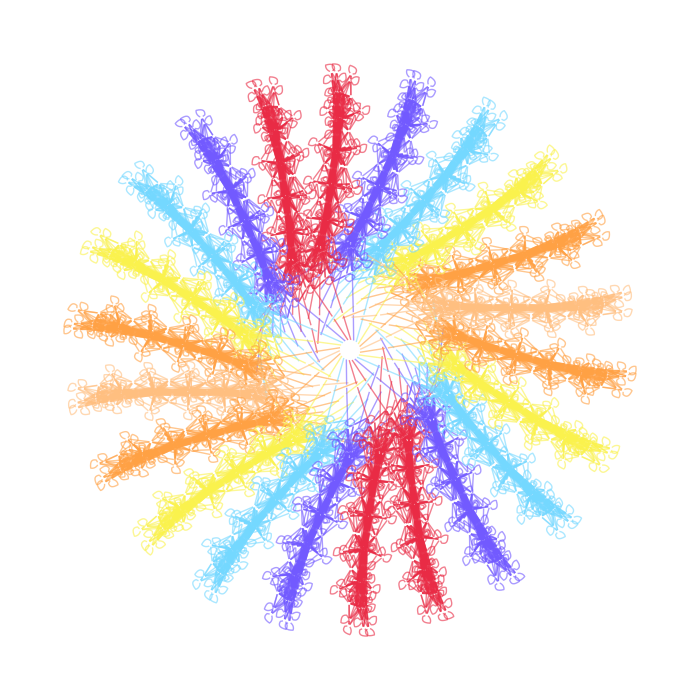

```mathematica
ResFun[m_]:=ResourceFunction["VertexCoordinateList"][AdjacencyGraph[ExampleData[{"Matrix",
m},"Matrix"]["PatternArray"]]];
RotM[a_,m_]:=RotationTransform[a,{0,0}]/@ResFun[m]//N;
RotMGraph[m_,n_]:=Table[GraphPlot[AdjacencyGraph[ExampleData[{"Matrix",m},
"Matrix"]["PatternArray"],VertexStyle->Transparent,
VertexShape->"",DirectedEdges->False],PlotStyle->Opacity[.6],
EdgeStyle->ColorData["BrightBands"][Cos[Pi*i/n]^2],
VertexCoordinates->RotM[i*Pi/n,m]],{i,2n}];
Show[RotMGraph["Morandini/robot",11],ImageSize->700]
```

Functions as Creativity Expression

```mathematica
Animate[Plot[Exp[-(-t+k/4)^2]*Sin[2Pi*(t+k/4)],
{t,-3,3},PlotRange->{-1,1},Filling->Axis,
PlotStyle->Hue[.05k],ImageSize->500,AspectRatio->1],{k,20},
AnimationRate->.5,AnimationRunning->False]
```

```mathematica
ComplexPlot3D[9z/(Cos[z^3]-Log[z^49]),{z,-3-3I,3+3I},
ColorFunction->"CyclicLogAbsArg",ClippingStyle->Transparent,
PlotStyle->Opacity[.8],PlotPoints->100,Boxed->False,Axes->False,
ImageSize->500,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ContourPlot[{Abs[Sin[(x+I*y)^5]]==1,
Abs[Cos[(x^3+I*y)^3]]==1},
{x,-1.8,1.8},{y,-1.8,1.8},Frame->False,
Background->RGBColor["silver"],PlotPoints->100,
ContourStyle->{White,Blue},ImageSize->500]
```

-Graphics-

def _(function=['(2t, t^2)','(7sin(t), 4cos(t)+6)','(2t cos(t)^2, t^2 cos(t)^2)']):
    n=10; var('t'); c=['#3636ff','#ff3636']; 
    if function=='(2t, t^2)':
        f = (2*t,t^2)
    elif function=='(7sin(t), 4cos(t)+6)':
        f = (7*sin(t),4*cos(t)+6)
    else: 
        f = (2*t*cos(t)^2,t^2*cos(t)^2)
    df = (f[0].diff(),f[1].diff()); d2f = (df[0].diff(),df[1].diff())
    def norm(g): return sqrt(sum(el^2 for el in g))
    normdf,normd2f = norm(df),norm(d2f); fnormal=(df[1]/normdf,-df[0]/normdf) 
    r=norm(df)^3/(df[1]*d2f[0]-df[0]*d2f[1]); centers=(f[0]+r*fnormal[0],f[1]+r*fnormal[1])
    print('f: x(t)=%s; y(t)=%s'%(f))
    p=parametric_plot(f,(t,-n,n),color=c[0],thickness=2)
    p+=parametric_plot(centers,(t,-n,n),color=c[1],thickness=3,linestyle='--')
    p+=sum(line2d([(f[0](t=i),f[1](t=i)),(centers[0](t=i),centers[1](t=i))], 
           thickness=1,rgbcolor=Color('silver').rgb()) for i in sxrange(-n,n,0.1))
    p.show(xmin=-8,xmax=8,ymin=-2,ymax=14,figsize=(5,5))
    
    norm(df)=2*sqrt(t^2 + 1); 
    norm(d2f)=2
    
    norm(df)=sqrt(49*cos(t)^2 + 16*sin(t)^2); 
    norm(d2f)=sqrt(16*cos(t)^2 + 49*sin(t)^2)
    
    norm(df)=2*sqrt((t^2*cos(t)*sin(t) - t*cos(t)^2)^2 + (2*t*cos(t)*sin(t) - cos(t)^2)^2); 
    norm(d2f)=2*sqrt((t^2*cos(t)^2 - t^2*sin(t)^2 + 4*t*cos(t)*sin(t) - cos(t)^2)^2 + 4*(t*cos(t)^2 - t*sin(t)^2 + 2*cos(t)*sin(t))^2)
    
    r=-2*(t^2 + 1)^(3/2); 
    fnormal=(t/sqrt(t^2 + 1), -1/sqrt(t^2 + 1))
    
    r=1/28*(49*cos(t)^2 + 16*sin(t)^2)^(3/2)/(cos(t)^2 + sin(t)^2); 
    fnormal=(-4*sin(t)/sqrt(49*cos(t)^2 + 16*sin(t)^2), -7*cos(t)/sqrt(49*cos(t)^2 + 16*sin(t)^2))
    
    r=2*((t^2*cos(t)*sin(t) - t*cos(t)^2)^2 + (2*t*cos(t)*sin(t) - cos(t)^2)^2)^(3/2)/(2*(t^2*cos(t)*sin(t) - t*cos(t)^2)*(t*cos(t)^2 - t*sin(t)^2 +
    +2*cos(t)*sin(t)) - (t^2*cos(t)^2 - t^2*sin(t)^2 + 4*t*cos(t)*sin(t) - cos(t)^2)*(2*t*cos(t)*sin(t) - cos(t)^2)); 
    fnormal=(-(t^2*cos(t)*sin(t) - t*cos(t)^2)/sqrt((t^2*cos(t)*sin(t) - t*cos(t)^2)^2 + (2*t*cos(t)*sin(t) - cos(t)^2)^2), 
    (2*t*cos(t)*sin(t) - cos(t)^2)/sqrt((t^2*cos(t)*sin(t) - t*cos(t)^2)^2 + (2*t*cos(t)*sin(t) - cos(t)^2)^2))

```mathematica
Simplify[-4Sin[t]/Sqrt[49Cos[t]^2+16Sin[t]^2]]
```

-(4 √2 Sin[t])/(√(65+33 Cos[2 t]))

```mathematica
SF={{2t,t^2},{7Sin[t],4Cos[t]+6},{2t*Cos[t]^2,t^2*Cos[t]^2}};
DSF=D[SF,t]; NDSF=Table[Sqrt[DSF[[i,1]]^2+DSF[[i,2]]^2],{i,3}];
D2SF=D[DSF,t];ND2SF=Table[Sqrt[D2SF[[i,1]]^2+D2SF[[i,2]]^2],{i,3}];
FNDSF=Table[{DSF[[i,2]]/NDSF[[i]],-DSF[[i,1]]/NDSF[[i]]},{i,3}] ;
RSF=Table[NDSF[[i]]^3/(DSF[[i,2]]*D2SF[[i,1]]-DSF[[i,1]]*D2SF[[i,2]]),{i,3}] ;
CSF=Table[{SF[[i,1]]+RSF[[i]]*FNDSF[[i,1]],SF[[i,2]]+RSF[[i]]*FNDSF[[i,2]]},{i,3}];
Table[ParametricPlot[{SF[[i]],CSF[[i]]},{t,-8,8},
PlotRange->{{-8,8},{-2,14}},ImageSize->{300,300}],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
F[t_]:={{2t,t^2},{7Sin[t],4Cos[t]+6},
{2t*Cos[t]^2,t^2*Cos[t]^2}};
DF[t_]:=D[F[t],t]; D2F[t_]:=D[DF[t],t];
NDF[t_]:=Table[Sqrt[DF[t][[i,1]]^2+DF[t][[i,2]]^2],{i,3}];
ND2F[t_]:=Table[Sqrt[D2F[t][[i,1]]^2+D2F[t][[i,2]]^2],{i,3}];
FNDF[t_]:=Table[{DF[t][[i,2]]/NDF[t][[i]],
-DF[t][[i,1]]/NDF[t][[i]]},{i,3}] ;
RF[t_]:=Table[NDF[t][[i]]^3/(DF[t][[i,
2]]*D2F[t][[i,1]]-DF[t][[i,1]]*D2F[t][[i,2]]),{i,3}] ;
CF[t_]:=Table[{F[t][[i,1]]+RF[t][[i]]*FNDF[t][[i,1]],
F[t][[i,2]]+RF[t][[i]]*FNDF[t][[i,2]]},{i,3}];
TF=Table[F[t],{t,-8,8,.1}];
TCF=Table[Evaluate[CF[t]],{t,-8,8,.1}];
Table[Show[ParametricPlot[{F[t][[i]],Evaluate[CF[t][[i]]]},
{t,-8,8},PlotStyle->Thick],
Table[ListLinePlot[Style[{TF[[k,i]],TCF[[k,i]]},
LightGray,Dashed]],{k,Length[TF[[All,i]]]}],
PlotRange->{{-8,8},{-2,14}},ImageSize->400],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

Surfaces as Creativity Expression

```mathematica
RT[a_,p_]:={RotationTransform[a,{0,1,1}]/@p[[1]]//N};
PT[p_,a_]:=Table[Tube[Table[(a/Pi)*RT[a,p][[1,p[[2,j,i]]]],
{i,Length[p[[2,j]]]}],.03],{j,Length[p[[2]]]}]
GT[p_,n_]:=Graphics3D[Table[{Hue[i/n],PT[p,2i*Pi/n]},{i,n}],
Boxed->False,ImageSize->600];
GT[BeveledPolyhedron[Dodecahedron[],.5],5]
```

-Graphics3D-

```mathematica
RL[a_,p_,v_]:={RotationTransform[a,v]/@p[[1]]};
PL[p_,a_,v_]:=
Table[Line[Table[RL[a,p,v][[1,p[[2,j,i]]]],
{i,Length[p[[2,j]]]}]],{j,Length[p[[2]]]}];
GL=Function[{p,n,v,col},
Graphics3D[Table[{ColorData[col][Cos[i*Pi/n]],
Style[PL[p,2i*Pi/n,v],Thick]},{i,n}],
Boxed->False,ImageSize->600]];
GL[BeveledPolyhedron[Tetrahedron[],.1],
11,{0,0,1},"CherryTones"]
```

-Graphics3D-

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
PP[p_]:=ExampleData[{"Geometry3D",p},"PolygonData"];
PV[p_,a_,w_,v_]:=RotationTransform[a,
w,v]/@ExampleData[{"Geometry3D",p},"VertexData"];
PPT[p_,a_,w_,v_]:=Polyhedron[PV[p,a,w,v],PP[p]];
Show[Graphics3D[Table[{FaceForm[{Cyan,Opacity[.3]}],
EdgeForm[RGBColor["slategray"]],PPT["Beethoven",
i*Pi/3,{0,0,1},{7,7,10}]},{i,6}],
Boxed->False,ImageSize->600]]
```

-Graphics3D-

```mathematica
PP[p_]:=ExampleData[{"Geometry3D",p},"PolygonData"];
PV[p_,a_,w_,v_]:=RotationTransform[a,
w,v]/@ExampleData[{"Geometry3D",p},"VertexData"];
PPT[p_,a_,w_,v_]:=Polyhedron[PV[p,a,w,v],PP[p]];
Graphics3D[Table[{FaceForm[{Cyan,Opacity[.3]}],EdgeForm[Green],
PPT["SpaceShuttle",i*Pi/2,{1,0,1},{10,10,5}]},{i,4}],
Boxed->False,ImageSize->800]
```

-Graphics3D-

```mathematica
Graphics3D[{FaceForm[{Blue,
Opacity[.03]}],EdgeForm[Gray],
Polyhedron[SortBy[ExampleData[{"Geometry3D",
"SpaceShuttle"},"VertexData"],Last],
Table[{i,i+1,i+2,i+3},{i,310}]]},
Boxed->False,ImageSize->600]
```

-Graphics3D-

Set Exercises

```mathematica
Manipulate[TableForm[{"P ∩ Q"->Intersection[P,Q],
"P ∩ R"->Intersection[P,R],
"Q ∩ R"->Intersection[Q,R],
"P ∩ Q ∩ R"->Intersection[P,Q,R]}],
{P,{{"a",3,2,"c",1,"ф","⎈","D"},
{"N",8,2,"c",1,"ф","⎈","D"}}},
{Q,{{"ф",7,"a","⎈",2,1,"B","θ"},
{"ф",5,"a","⎈",2,8,"N","θ"}}},
{R,{{8,"N","a","θ",4,"P","⎈","r"},
{1,"N","a","θ",7,"P","⎈","r"}}}]
```

```mathematica
Manipulate[TableForm[{"P ∪ Q "->Union[P,Q],
"P ∪ R"->Union[P,R],
"Q ∪ R"->Union[Q,R],
"P ∪ Q ∪ R"->Union[P,Q,R]}],
{P,{{"a",3,2,"c",1,"ф","⎈","D"},
{"N",8,2,"c",1,"ф","⎈","D"}}},
{Q,{{"ф",7,"a","⎈",2,1,"B","θ"},
{"ф",5,"a","⎈",2,8,"N","θ"}}},
{R,{{8,"N","a","θ",4,"P","⎈","r"},
{1,"N","a","θ",7,"P","⎈","r"}}}]
```

Exercises with Linear Models

```mathematica
data=Values[Normal[ResourceData["Global Obesity Rates"][[All,3;;4]]]];
lm=LinearModelFit[data,x,x]; lm[{"BestFit","ParameterTable","RSquared"}]
TableForm[{ListPlot[{data,Table[{x,lm["BestFit"]},{x,0,.5,.005}]},ImageSize->400,
PlotStyle->{Gray,{Blue,Opacity[.1]}},Filling->{1->{2}}],
ListPlot[lm["CookDistances"],Filling->Axis,ImageSize->400],
ListPlot[Transpose[{data[[All,1]],lm["CookDistances"]}],
ImageSize->400,Filling->Axis]}]
```

{0.08545+1.46759 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.08545 | 0.00479706 | 17.813 | 5.4036×10^-43
x | 1.46759 | 0.0468168 | 31.3474 | 1.0519×10^-78,0.832297}

-Graphics-
-Graphics-
-Graphics-

HTML & CSS Elements as Creativity Expression

```mathematica
EmbeddedHTML["<style>@import url('https://fonts.googleapis.com/css?family=Miss Fajardose');</style>
<script>function f2c(f) {document.getElementById('demo').innerHTML=(5/9)*(f-32);}</script>
<button style='background-color:white; color:#3636ff; font-family:Miss Fajardose; font-size:300%;' 
onclick='f2c(86);' type='button'>
Evaluate the javascript code for converting the Fahrenheit temperature 86 &ordm; to Celsius</button>
<p id='demo' style='color:#3636ff; font-family:Miss Fajardose; font-size:200%;'></p>",ImageSize->{1000,200}]
```

Null<style>@import url('https://fonts.go…Miss Fajardose; font-size:200%;'></p><style>@import url('https://fonts.googleapis.com/css?family=Miss Fajardose');</style>
<script>function f2c(f) {document.getElementById('demo').innerHTML=(5/9)*(f-32);}</script>
<button style='background-color:white; color:#3636ff; font-family:Miss Fajardose; font-size:300%;' 
onclick='f2c(86);' type='button'>
Evaluate the javascript code for converting the Fahrenheit temperature 86 &ordm; to Celsius</button>
<p id='demo' style='color:#3636ff; font-family:Miss Fajardose; font-size:200%;'></p>